```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils","plot_utils.m"}];
<<(plotUtils)
```

```mathematica
Conv[rule_]:=Module[{vars=rule/.Rule[a_,b_]->a},
Table[d[[n]]/.rule,{}]
]
```

```mathematica
(*error=0.0001, p=1*)
sequence=U[-Δ1,Ω1].U[-Δ2,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
rule1={Δ1->-0.9267,Δ2->0.0227,Ω1->0.6750};(*N=4, BW=0.2, area=2.7π*)
prob1=GetProbFn[sequence,rule1];
text1=text["X4",{0.7,0.55}];

sequence=U[-Δ1,Ω1].U[-Δ2,Ω1].U[0,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
rule2={Δ1->0.8746,Δ2->0.1360,Ω1->0.5498};(*N=5, BW=0.2, area=2.75π*)
prob2=GetProbFn[sequence,rule2];
text2=text["X5",{0.7,0.70}];

sequence=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
{Δ1->0.1922,Δ2->-0.3621,Δ3->-0.6779,Ω1->0.4537};(*N=6, BW=0.2, area=2.72π*)
rule3={Δ1->0.5918,Δ2->0.5951,Δ3->-0.7717,Ω1->0.6118};(*N=6, BW=0.3, area=3.67π*)
prob3=GetProbFn[sequence,rule3];
text3=text["X6",{0.7,0.92}];

sequence=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[0,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
{Δ1->-0.1770,Δ2->0.136,Δ3->0.6645,Ω1->0.3877};(*N=7, BW=0.2, area=2.71π*)
rule4={Δ1->0.9507,Δ2->0.1825,Δ3->0.1805,Ω1->0.5153};(*N=7, BW=0.3, area=3.61π*)
prob4=GetProbFn[sequence,rule4];
text4=text["X7",{0.7,0.82}];
(*6 is better*)
```

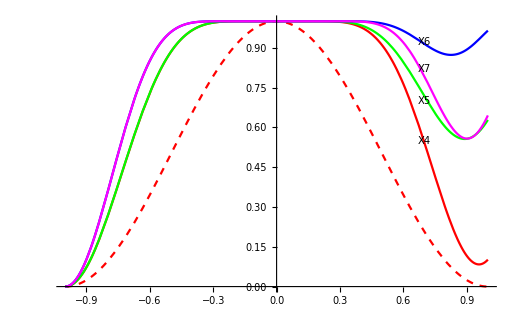

```mathematica
path=FileNameJoin[{NotebookDirectory[],"paper"}];
fname=FileNameJoin[{path,"multiple_BBs.pdf"}];

pl=Plot[{single[1],prob1,prob2,prob3,prob4},{ϵ,-1,1},Epilog->{text1,text2,text3,text4},PlotStyle->{{Dashed,Red},Red,Green,Blue,Magenta}]
Export[fname,pl]
```